```mathematica
<<InitPackages`
DateString[]
```

Fri 5 Aug 2011 19:50:28

## Calculation of π Using a Numerical Integraltion

```mathematica
MPAFE[HoldForm@∫_0^1 4/(1+x^2)ⅆx,MPEvaluateInt,All]
```

∫_0^1 4/(1+x^2)ⅆx==π

## Standard Normal Distribution

```mathematica
Subscript[φ, μ,σ^2][x]==1/(σ √(2π))ⅇ^((-(x-μ)^2)/(2 σ^2))
MPMAF[%,MPEliminate,{At[2],{μ==0,σ^2==1},{μ,σ}}]
```

φ_(μ,σ^2)[x]==(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

φ_(μ,σ^2)[x]==(ⅇ^(-x^2/2))/(√(2 π))

φ_(μ,σ^2)[x]==(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) √(σ^2))

{0.892062 ⅇ^(-2.5 x^2),0.398942 ⅇ^(-0.5 x^2),0.178412 ⅇ^(-0.1 x^2),0.56419 ⅇ^(-1. (2+x)^2)}

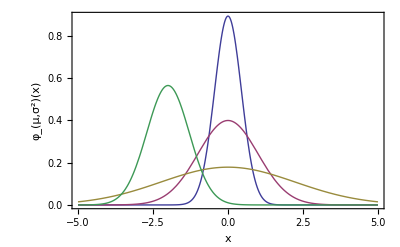

```mathematica
Subscript[φ, μ,σ^2][x]==1/(√(2π σ^2))ⅇ^((-(x-μ)^2)/(2 σ^2))
%[[2]]//{Tooltip[#/.{μ->0,σ^2->0.2,σ^-2->0.2^-1},"μ==0,σ^2==0.2"],Tooltip[#/.{μ->0,σ^2->1.0,σ^-2->1.0^-1},"μ==0,σ^2==1.0"],Tooltip[#/.{μ->0,σ^2->5.0,σ^-2->5.0^-1},"μ==0,σ^2==5.0"],Tooltip[#/.{μ->-2,σ^2->0.5,σ^-2->0.5^-1},"μ==-2,σ^2==0.5"]}&
Plot[%,{x,-5,5},Axes->False,Frame->True,PlotRange->All,FrameLabel->{x,Subscript[φ, μ,σ^2][x]}]
```